H={0.577552, 3.21443, 11.4517, -0.448729, 0.233417, 8.69148, 12.5331, 13.0909, 10.8223, 10.5191}

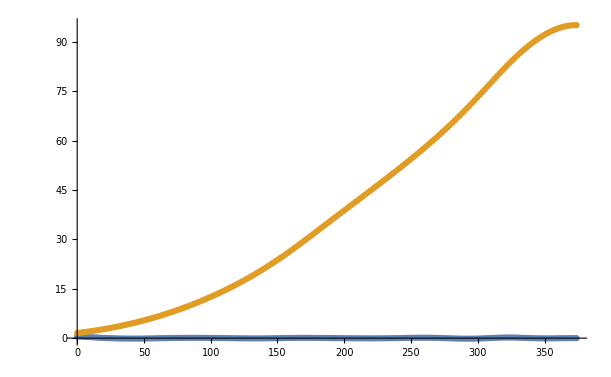

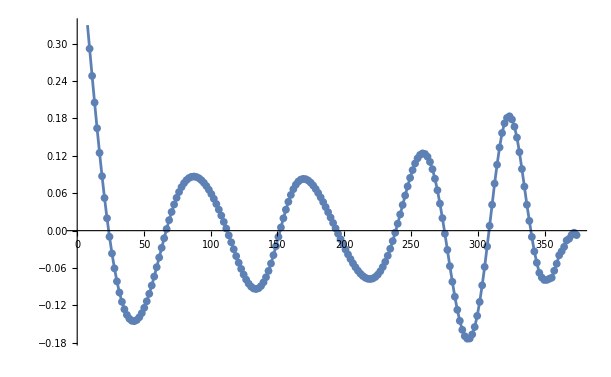

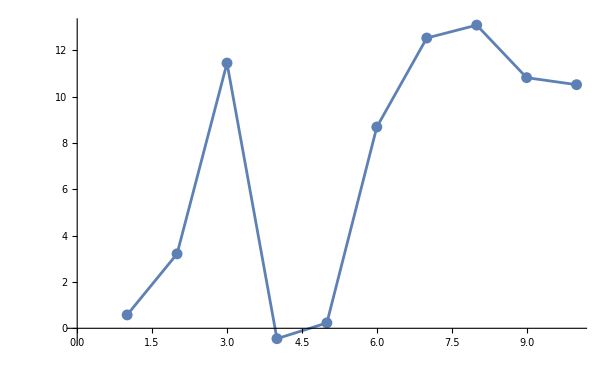

```mathematica
(*获取当前 Notebook 的目录*)
currentDirectory=NotebookDirectory[];
(*设置当前工作目录为 Notebook 目录*)
SetDirectory[currentDirectory];

Inputdata =Table[ToExpression[ Partition[StringReplace[StringSplit[Import["data\\" <> ToString[i] <>".txt"]],"e"->"*10^"],2]],{i,1,10,1}];
HeatNum = 10;
DataxNum = Length[Inputdata[[1]]];
M=Table[Inputdata[[i]][[j]][[2]],{i,1,10,1},{j,1,DataxNum,1}]*10^9//Transpose;
Inputdata =ToExpression[ Partition[StringReplace[StringSplit[Import["data\\heat source.txt"]],"e"->"*10^"],2]];
datax = Map[First,Inputdata]*10^3;
K= -Map[Last,Inputdata]*10^9;
H=LeastSquares[M,K];
Print["H="<>ToString[H]]

ListPlot[{Partition[Riffle[datax,M.H-K],2],Partition[Riffle[datax,-K],2]},Mesh->All,Joined->True]
ListPlot[Partition[Riffle[datax,M.H-K],2],Mesh->All,Joined->True]
ListPlot[{H},Mesh->All,Joined->True]
```